# Quantum Teleportation in Wolfram Model

Muhammad Taufiq Murtadho

Korea Advanced Institute of Science and Technology

Abstract: Entanglement is a valuable resource for many quantum communication tasks. One example of such tasks is quantum teleportation where a quantum state is transferred between two spatially separated parties by performing only local operations and classical communication (LOCC). In this project, we explore the analog of quantum teleportation in the Wolfram model by looking at string substitution systems. In other words, we investigate whether we can teleport a string from one spatial location to the other by using entanglement in branchial space. 

Objective: Generate events on a string multiway system that can be interpreted as a quantum teleportation phenomenon.

Computational Plan/Strategy: First, we identify a string transformation pattern that correspond to quantum teleportation. Then, we develop a program to scan through a multiway system to spot the pattern. Then, we apply the program to a class of string substitution rules that can potentially display quantum teleportation phenomenon.

## Research Notes/Documentation

#### Knuth-Bendix Completion

```mathematica
ResourceFunction["MultiwaySystem"][{"X"-> "AXA","X"-> "BXB"},"XC",2,"EvolutionCausalGraph"]
```

-Graphics-

```mathematica
ResourceFunction["MultiwaySystem"][{"X"-> "AXA","X"-> "BXB"},"XC",5,"EvolutionCausalGraphStructure"]
```

-Graphics-

```mathematica
ResourceFunction["MultiwaySystem"][{"X"-> "AXA","X"-> "BXB"},"XC",2,"AllStatesBranchialGraph"]
```

-Graphics-

```mathematica
ResourceFunction["CanonicalKnuthBendixCompletion"][{"X"-> "AXA","X"-> "BXB"}]
```

{AXA→BXB,BXB→AXA}

This means, by adding an equivalence relation {AXA→BXB,BXB→AXA}, we can generate a causal invariant system which guarantees that “AXA” and “BXB” would be resolved in some future time. This completion procedure is interpreted as a projection from “AXA” to “BXB” and vice versa. The states to which they converge correspond to the possible measurement outcomes of this projection.

Before Knuth-Bendix completion

```mathematica
ResourceFunction["MultiwaySystem"][{"X"-> "AXA","X"-> "BXB"},"XC",3,"StatesGraph"]
ResourceFunction["MultiwaySystem"][{"X"-> "AXA","X"-> "BXB"},"XC",3,"EvolutionGraph"]
```

-Graphics-

-Graphics-

After Knuth-Bendix completion

```mathematica
ResourceFunction["MultiwaySystem"][{"X"-> "AXA","X"-> "BXB","AXA"->"BXB","BXB"->"AXA"},"XC",3,"StatesGraph"]
```

-Graphics-

```mathematica
ResourceFunction["MultiwaySystem"][{"X"-> "AXA","X"-> "BXB","AXA"->"BXB","BXB"->"AXA"},"XC",3,"CausalGraph"]
ResourceFunction["MultiwaySystem"][{"X"-> "AXA","X"-> "BXB","AXA"->"BXB","BXB"->"AXA"},"XC",3,"CausalGraphInstances"]
```

-Graphics-

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ResourceFunction["MultiwaySystem"][{"X"-> "AXA","X"-> "BXB","AXA"->"BXB","BXB"->"AXA"},"XC",3,"EvolutionGraphStructure",VertexStyle-> {(1-> "AXAC")-> Red, (1-> "BXBC")-> Red,(3-> "AAXAAC")-> Red, (3-> "BBXBBC")-> Red,(3-> "BAXABC")-> Red, (3-> "ABXBAC")-> Red}]
```

-Graphics-

The red vertices on the last step are the states to which AXAC and BXBC converge. They correspond to our possible measurement outcomes.

```mathematica
ResourceFunction["MultiwaySystem"][{"X"-> "AXA","X"-> "BXB","AXA"->"BXB","BXB"->"AXA"},"XC",3,"BranchialGraph"]
```

-Graphics-

The measurement outcomes are causally-independent (not entangled) from each other.

```mathematica
ResourceFunction["MultiwaySystem"][{"X"-> "AXA","X"-> "BXB","AXA"->"BXB","BXB"->"AXA"},"XC",3,"EvolutionGraph"]
```

-Graphics-

```mathematica
ResourceFunction["CausalInvariantQ"][{"X"-> "AXA","X"-> "BXB","AXA"->"BXB","BXB"->"AXA"},"XC",3]
ResourceFunction["CanonicalBranchPairs"][{"X"-> "AXA","X"-> "BXB","AXA"->"BXB","BXB"->"AXA"},2,"GiveResolvents"-> True]
```

True

<|Resolved→{{AAXAA,ABXBA}→AAAAXAAAA,{AAXAA,BXB}→AAAAXAAAA,{AAXAAXA,ABXBAXA}→AAAAXAAAAXA,{AAXAAXA,AXAAXAA}→AAAXAAAAXAA,{AAXAAXA,AXABXBA}→AAAXAAAAXAA,{AAXAAXA,AXBXB}→AAAAXAAAAXA,{AAXAAXA,BXBXA}→AAAAXAAAAXA,{ABXBA,BXB}→AAAXAAA,{ABXBAXA,AXAAXAA}→AAAXAAAAXAA,{ABXBAXA,AXABXBA}→AAAXAAABXBA,{ABXBAXA,AXBXB}→AAAXAAAXA,{ABXBAXA,BXBXA}→AAAXAAAXA,{AXA,BAXAB}→BAAAXAAAB,{AXA,BBXBB}→BAAXAAB,{AXA,BXB}→AAAXAAA,{AXAAXAA,AXABXBA}→AAAXAAAAXAA,{AXAAXAA,AXBXB}→AAAXAAAAXAA,{AXAAXAA,BXBXA}→AAAXAAAAXAA,{AXABXBA,AXBXB}→AAAXAAABXBA,{AXABXBA,BXBXA}→AAAXAAABXBA,{AXAXB,BAXABXB}→BAAAXAAABXB,{AXAXB,BBXBBXB}→BAAXAABXB,{AXAXB,BXAXA}→AAAXAAAXB,{AXAXB,BXBAXAB}→AAXAAAXAB,{AXAXB,BXBBXBB}→AAXAAAXAB,{AXBXB,BXBXA}→AAAXAABXB,{BAXAB,BBXBB}→BAAAXAAAB,{BAXABXB,BBXBBXB}→BAAAXAAABXB,{BAXABXB,BXAXA}→BAAAXAAABXB,{BAXABXB,BXBAXAB}→BAAXAABAXAB,{BAXABXB,BXBBXBB}→BAAXAABAXAB,{BBXBBXB,BXAXA}→BAAXAAAXA,{BBXBBXB,BXBAXAB}→BAAXAABAXAB,{BBXBBXB,BXBBXBB}→BAAXAABBXBB,{BXAXA,BXBAXAB}→AAXAAAXAB,{BXAXA,BXBBXBB}→AAXAABXBB,{BXBAXAB,BXBBXBB}→AAXAAAXAB},Unresolved→{}|>

```mathematica
ResourceFunction["CausalInvariantQ"][{"X"-> "AXA","X"-> "BXB"},"XC",3]
ResourceFunction["CanonicalBranchPairs"][{"X"-> "AXA","X"-> "BXB"},5,"GiveResolvents"-> True]
```

False

<|Resolved→{},Unresolved→{{AXA,BXB}}|>

The difference between “canonical” Knuth-Bendix completion and Knuth-Bendix completion

Canonical Knuth-Bendix completion is minimal and initial condition independent.

```mathematica
ResourceFunction["KnuthBendixCompletion"][{"X"-> "AXA","X"-> "BXB"},"XC",2]
```

```mathematica
{"AAXAAC"->"ABXBAC","ABXBAC"->"AAXAAC","AXAC"->"BXBC","BXBC"->"AXAC","BAXABC"->"BBXBBC","BBXBBC"->"BAXABC"}
```

```mathematica
ResourceFunction["MultiwaySystem"][{"X"-> "AXA","X"-> "BXB","AXA"->"BXB","BXB"->"AXA","AAXAAC"->"ABXBAC","ABXBAC"->"AAXAAC","AXAC"->"BXBC","BXBC"->"AXAC","BAXABC"->"BBXBBC","BBXBBC"->"BAXABC"},"XC",2,"StatesGraph"]
```

-Graphics-

#### Quantum Teleportation Scheme (1st attempt, FAILED)

In the usual quantum teleportation scheme, we have a projection from (00+11 )ψ →ψBell . Then, the analogue of quantum teleportation in a string multiway system is a projection of branch pair of the form

```mathematica
ResourceFunction["MultiwaySystem"][{"X"-> "AXA","X"-> "BXB"},"XC",1,"EvolutionCausalGraph"]
ResourceFunction["MultiwaySystem"][{"X"-> "AXA","X"-> "BXB"},"XC",1,"BranchialGraph"]
```

-Graphics-

-Graphics-

X is just a string coordinate marker which plays a role of spatial separation. After the teleportation protocol - Knuth Bendix completion - the branch pairs is resolved into 4 possible states {CXAB, CXBA, CXAA, CXBB} where AB, BA, AA, BB now encodes

```mathematica
ResourceFunction["MultiwaySystem"][{"AXAC"-> "CXAB","AXAC"-> "CXBA","AXAC"-> "CXAA", "AXAC"-> "CXBB","BXBC"-> "CXBA","BXBC"-> "CXAB","BXBC"-> "CXAA", "BXBC"-> "CXBB"},{"AXAC","BXBC"},1,"StatesGraph"]
```

-Graphics-

Our task is to find string substitution rule that generate entangled branch pair of the form {AXAC, BXBC} and its Canonical Knuth-Bendix completion would resolve them into {CXAB, CXBA, CXAA, CXBB}.

```mathematica
ResourceFunction["MultiwaySystem"][{"X"-> "AXA","X"-> "BXB","AC"-> "CA","BC"-> "CA","XC"-> "CX"},"XC",3,"StatesGraph"]
ResourceFunction["MultiwaySystem"][{"X"-> "AXA","X"-> "BXB","AC"-> "CA","BC"-> "CA","XC"-> "CX"},"XC",3,"BranchialGraph"]
```

-Graphics-

-Graphics-

```mathematica
ResourceFunction["CanonicalKnuthBendixCompletion"][{"X"-> "AXA","X"-> "BXB","AC"-> "CA","BC"-> "CA","XC"-> "CX"}]
```

{AXA→BXB,BXB→AXA,AXAC→BXBC,BXBC→AXAC,AXAC→CX,CX→AXAC,BXBC→CX,CX→BXBC}

```mathematica
ResourceFunction["MultiwaySystem"][{"X"-> "AXA","X"-> "BXB","AC"-> "CA","BC"-> "CA","XC"-> "CX","AXA"->"BXB","BXB"->"AXA","AXAC"->"BXBC","BXBC"->"AXAC","AXAC"->"CX","CX"->"AXAC","BXBC"->"CX","CX"->"BXBC"},"XC",3,"CausalGraphStructure"]
```

-Graphics-

#### QuantumToMultiwaySystem

Jonathan Gorard has built a framework named “QuantumToMultiwaySystem” to simulate quantum evolution in a multiway system which is available in function repository.

Hadamard gate

```mathematica
ResourceFunction["QuantumToMultiwaySystem"][{{1,1},{1,-1}},{1,0},3,"EvolutionGraph","IncludeStatePathWeights"-> True, VertexLabels-> "VertexWeight"]
```

-Graphics-

```mathematica
rule1 = ResourceFunction["QuantumToMultiwaySystem"][<|"Operator"-> {{1,1},{1,-1}},"Basis"-> IdentityMatrix[2]|>]
```

{{1, 0}→{1, 0},{1, 0}→{0, 1},{0, 1}→{1, 0},{0, 1}→{0, -1},{0, -1}→{0, 1},{-1, 0}→{-1, 0},{-1, 0}→{0, -1},{0, -1}→{-1, 0},{I, 0}→{I, 0},{I, 0}→{0, I},{0, I}→{I, 0},{0, I}→{0, -I},{0, -I}→{0, I},{-I, 0}→{-I, 0},{-I, 0}→{0, -I},{0, -I}→{-I, 0}}

```mathematica
ResourceFunction["MultiwaySystem"][rule1,ToString/@{{1,0},{I,0}},2,"BranchialGraph"]
```

-Graphics-

```mathematica
ResourceFunction["CanonicalKnuthBendixCompletion"][rule1]
```

{{0, -1}→{-1, 0},{-1, 0}→{0, -1},{0, -1}→{1, 0},{1, 0}→{0, -1},{0, 1}→{-1, 0},{-1, 0}→{0, 1},{0, 1}→{1, 0},{1, 0}→{0, 1},{0, -I}→{-I, 0},{-I, 0}→{0, -I},{0, -I}→{I, 0},{I, 0}→{0, -I},{0, I}→{-I, 0},{-I, 0}→{0, I},{0, I}→{I, 0},{I, 0}→{0, I}}

```mathematica
ResourceFunction["QuantumToMultiwaySystem"][{{1,1},{1,-1}},{1,0},4,"EvolutionBranchialGraph"]
```

-Graphics-

#### Quantum Teleportation Scheme (2nd attempt, FAILED)

Measurement under different basis correspond to different foliation of multiway system. In order to simulate both computational basis and Bell basis using string, we first need to make a dictionary.

Computational Basis: X → Empty space, C → Unknown qubit state, AA → 00, BB → 11, AB → 01,  BA→10

Bell Basis: X → Empty space, C → Unknown qubit state, AA → 00+11, BB → 00-11, AB → 01+10,  BA→01-10

Consider the following multiway system

```mathematica
ResourceFunction["MultiwaySystem"][{"A"-> "BCX", "B"-> "CXA"},{"AB"},1,"EvolutionCausalGraph",AspectRatio-> 0.3]
```

-Graphics-

The two states are spatially-separated and therefore causally-independent in a sense that the updating events leading to them can be consistently applied at the same time (they act on different part of the substring). However, they are entangled because in a multiway system, they can have causal relation (in some future time) by virtue of their common ancestor.

```mathematica
ResourceFunction["MultiwaySystem"][{"A"-> "BCX", "B"-> "CXA"},{"AB"},4,"EvolutionCausalGraphStructure",AspectRatio-> 0.3]
ResourceFunction["MultiwaySystem"][{"A"-> "BCX", "B"-> "CXA"},{"AB"},6,"EvolutionCausalGraphStructure",AspectRatio-> 0.3]
```

-Graphics-

-Graphics-

Quantum measurement correspond to foliation in the multiway system. Different measurement basis correspond to different choice of foliation.

```mathematica
CloudGet["https://wolfr.am/LbfUewoW"];
Magnify[Graph[ResourceFunction["MultiwaySystem"][{"A"-> "BCX", "B"-> "CXA"},{"AB"},1,"StatesGraph"],GraphLayout->"LayeredDigraphEmbedding",VertexCoordinates->(Thread[VertexList[#]->GraphEmbedding[#,Automatic,2]]&[ResourceFunction["MultiwaySystem"][{"A"-> "BCX", "B"-> "CXA"},{"AB"},1,"StatesGraph"]]),Epilog->{Purple,AbsoluteThickness[1.5],straightFoliationLines[{1,1.2},{.1,.4}]}],.8]
```

-Graphics-

Interpretation:
The first two letter is Alice’s qubits, X (third letter) is spatial separation, and the last letter is Bob’s qubit. In the computational basis frame, we start from a separable state 01. Then, we produce spatially separated Bell state of the form (00+11) and attach an unknown qubit state C to Alice’s state. Transforming into Bell quantum measurement frame, we can project ACXA to AB by performing Knuth-Bendix completion, which we interpret as Bell measurement carried out by Alice. If quantum teleportation occurs, then the final state of the system is expected to be ABXC.

```mathematica
ResourceFunction["MultiwaySystem"][{"A"-> "BCX", "B"-> "CXA","AB"-> "ACXA","ACXA"-> "AB"},"AB",3,"StatesGraph"]
ResourceFunction["MultiwaySystem"][{"A"-> "BCX", "B"-> "CXA","AB"-> "ACXA","ACXA"-> "AB"},"AB",3,"CausalGraph"]
```

-Graphics-

-Graphics-

In this particular system, forcing equivalence relation between AB and ACXA does not lead to causal invariance and thus it is not a valid projection operator. In the system, we are looking for, the resulting system must be causal invariant after the measurement.

#### The above interpretation is again, wrong. The reason is because if we define foliation as above, ACXA and AB are considered to be simultaneous and thus they must be causally-independent. This is impossible given that in another frame AB is the ancestor of ACXA and thus they are causally dependent.

```mathematica
ResourceFunction["MultiwaySystem"][{"X"-> "AB","X"-> "BA","X"-> "BB","X"-> "AA","A"->"BC","A"-> "CA","B"-> "BC","B"-> "CA"},"X",2,"EvolutionCausalGraph"]
```

-Graphics-

```mathematica
ResourceFunction["MultiwaySystem"][{"X"-> "AB","X"-> "BA","X"-> "BB","X"-> "AA","A"->"BC","A"-> "CA","B"-> "BC","B"-> "CA"},"X",2,"BranchialGraph"]
```

-Graphics-

BCB and ACA are like Bell-state with spatial separation (separated by unknown state C)

```mathematica
completion = ResourceFunction["KnuthBendixCompletion"][{"X"-> "AB","X"-> "BA","X"-> "BB","X"-> "AA","A"->"BC","A"-> "CA","B"-> "BC","B"-> "CA"},"X",2]
```

{AB→BA,BA→AB,ABC→ACA,ACA→ABC,ABC→BCA,BCA→ABC,ABC→BCB,BCB→ABC,ABC→CAA,CAA→ABC,ABC→CAB,CAB→ABC,ACA→BCA,BCA→ACA,ACA→BCB,BCB→ACA,ACA→CAA,CAA→ACA,ACA→CAB,CAB→ACA,BBC→BCA,BCA→BBC,BBC→BCB,BCB→BBC,BBC→CAA,CAA→BBC,BBC→CAB,CAB→BBC,BCA→BCB,BCB→BCA,BCA→CAA,CAA→BCA,BCA→CAB,CAB→BCA,BCB→CAB,CAB→BCB}

```mathematica
ResourceFunction["MultiwaySystem"][Join[{"X"-> "AB","X"-> "BA","X"-> "BB","X"-> "AA","A"->"BC","A"-> "CA","B"-> "BC","B"-> "CA"},completion],"X",4,"CausalGraphInstances",MaxItems-> 7]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ResourceFunction["MultiwaySystem"][Join[{"X"-> "AB","X"-> "BA","X"-> "BB","X"-> "AA","A"->"BC","A"-> "CA","B"-> "BC","B"-> "CA"},completion],"X",3,"CausalGraphStructure"]
```

-Graphics-

```mathematica
ResourceFunction["MultiwaySystem"][Join[{"X"-> "AB","X"-> "BA","X"-> "BB","X"-> "AA","A"->"BC","A"-> "CA","B"-> "BC","B"-> "CA"},completion],"X",3,"CausalInvariantQ"]
```

True

#### Quantum Teleportation Scheme (3rd attempt) A PARADIGM SHIFT

Since a quantum measurement is no longer identified with a single state projection, but instead a completion process on the whole branchial hypersurface, the analogue of usual quantum teleportation protocol would not work. A paradigm shift is needed. I propose the following. We start from an initial condition “AXBC” where AB denotes one of the Bell basis state (we can also use BA, AA, BB). Now, we evolve the whole tripartite state according to some rule. After some time steps, perform Knuth-Bendix completion. The task is to find the rule and the corresponding time step in which the history of the system converge to CXAB | CXBA | CXAA | CXBB. If such rule exist, we say that it correspond to a quantum teleportation protocol. Now, there is subtlety in this approach. We need to prove that to reach the target state, entanglement is needed. 

This approach has unclear interpretation and it seems impossible to do without introducing a “cheating” rule such as “A”→”C” when we want to teleport AXBC → CXAB.

```mathematica
completion =ResourceFunction["MultiwaySystem"][{"A"-> "CA","A"-> "CB","AB"-> "C"},"ABC",3,"EvolutionCausalGraphStructure"]
```

-Graphics-

```mathematica
completion =ResourceFunction["KnuthBendixCompletion"][{"A"-> "CA","A"-> "CB"},"ABC",3]
```

{CABC→CBBC,CBBC→CABC,CCABC→CCBBC,CCBBC→CCABC,CCCABC→CCCBBC,CCCBBC→CCCABC}

```mathematica
ResourceFunction["MultiwaySystem"][Join[{"A"-> "CA","A"-> "CB"},completion],"ABC",4,"CausalGraphInstances",MaxItems-> 5]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Is local rule always terminate as normal form?

```mathematica
ResourceFunction["MultiwaySystem"][{"C"-> "B","C"-> "A","B"-> "C","A"-> "B","B"-> "A","A"-> "C"},"AXBC",3,"StatesGraph"]
```

-Graphics-

Here, we found states like CXBA and CXBB which can potentially represent quantum teleportation phenomenon. Note that, we do not impose rule “A”→”C”, “C” can only appear in the first letter because of the connection “A”→”B” and “B”→”C” which is what typically happen in teleportation.

```mathematica
ResourceFunction["MultiwaySystem"][{"C"-> "B","C"-> "A","B"-> "C","A"-> "B","B"-> "A"},"AXBC",3,"BranchialGraph"]
```

-Graphics-

```mathematica
cmp = ResourceFunction["KnuthBendixCompletion"][{"C"-> "B","C"-> "A","B"-> "C","A"-> "B","B"-> "A"},"ABXC",4];
```

```mathematica
ResourceFunction["MultiwaySystem"][Join[{"C"-> "B","C"-> "A","B"-> "C","A"-> "B","B"-> "A"},cmp],"AXBC",4,"CausalInvariantQ"]
```

True

```mathematica
ResourceFunction["MultiwaySystem"][Join[{"C"-> "B","C"-> "A","B"-> "C","A"-> "B","B"-> "A"},cmp],"AXBC",4,"CausalGraphInstances",MaxItems-> 10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
stripMetadata[expression_]:=If[Head[expression]===Rule,Last[expression],expression];Graph[ResourceFunction["MultiwaySystem"][{"C"-> "B","C"-> "A","B"-> "C","A"-> "B","B"-> "A"},{"AXBC"},3,"StatesGraph"],VertexShapeFunction->{Alternatives@@VertexList[ResourceFunction["GenerationalMultiwaySystem"][{"C"-> "B","C"-> "A","B"-> "C","A"-> "B","B"-> "A"},{"AXBC"},2,"StatesGraph"]]->(Text[Framed[Style[stripMetadata[#2],Hue[0,1,0.48]],Background->Directive[Opacity[.6],Hue[0,0.45,0.87]],FrameMargins->{{2,2},{0,0}},RoundingRadius->0,FrameStyle->Directive[Opacity[0.5],Hue[0,0.52,0.8200000000000001]]],#1,{0,0}]&)}]
ResourceFunction["MultiwaySystem"][{"C"-> "B","C"-> "A","B"-> "C","A"-> "B","B"-> "A"},"AXBC",3,"StatesGraph"]
```

-Graphics-

-Graphics-

```mathematica
ResourceFunction["MultiwaySystem"][{"C"-> "B","C"-> "A","B"-> "C","A"-> "B"},"AXBC",3,"StatesGraph"]
```

-Graphics-

```mathematica
cmp2 =ResourceFunction["KnuthBendixCompletion"][{"C"-> "B","C"-> "A","B"-> "C","A"-> "B"},"AXBC",2] 
ResourceFunction["MultiwaySystem"][Join[{"C"-> "B","C"-> "A","B"-> "C","A"-> "B"},cmp2],"AXBC",3,"CausalInvariantQ"]
```

{AXAC→AXBC,AXBC→AXAC,AXAC→AXCA,AXCA→AXAC,AXAC→AXCB,AXCB→AXAC,AXAC→BXCC,BXCC→AXAC,AXBB→AXCA,AXCA→AXBB,AXBB→BXBA,BXBA→AXBB,AXBC→AXCA,AXCA→AXBC,AXBC→AXCB,AXCB→AXBC,AXBC→BXBB,BXBB→AXBC,AXBC→BXCC,BXCC→AXBC,AXCA→AXCB,AXCB→AXCA,AXCA→BXBA,BXBA→AXCA,AXCA→BXCC,BXCC→AXCA,AXCB→BXBB,BXBB→AXCB,AXCB→BXCC,BXCC→AXCB,BXBA→BXBB,BXBB→BXBA,BXBA→BXCC,BXCC→BXBA,BXBA→CXBC,CXBC→BXBA,BXBB→BXCC,BXCC→BXBB,BXBB→CXBC,CXBC→BXBB,BXCC→CXBC,CXBC→BXCC}

True

```mathematica
ResourceFunction["MultiwaySystem"][Join[{"C"-> "B","C"-> "A","B"-> "C","A"-> "B"},cmp2],"AXBC",4,"CausalGraphInstances",MaxItems-> 10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
cmp = ResourceFunction["KnuthBendixCompletion"][{"A"-> "B","B"-> "A","B"-> "C","C"->"B"},"AXBC",2]
```

{AXAB→AXBA,AXBA→AXAB,AXAB→AXBC,AXBC→AXAB,AXAB→AXCB,AXCB→AXAB,AXAB→BXAC,BXAC→AXAB,AXAB→BXBB,BXBB→AXAB,AXBA→AXBC,AXBC→AXBA,AXBA→AXCB,AXCB→AXBA,AXBA→BXBB,BXBB→AXBA,AXBC→AXCB,AXCB→AXBC,AXBC→BXAC,BXAC→AXBC,AXBC→BXBB,BXBB→AXBC,AXBC→BXCC,BXCC→AXBC,AXBC→CXBC,CXBC→AXBC,AXCB→BXBB,BXBB→AXCB,AXCB→BXCC,BXCC→AXCB,BXAC→BXBB,BXBB→BXAC,BXAC→BXCC,BXCC→BXAC,BXAC→CXBC,CXBC→BXAC,BXBB→BXCC,BXCC→BXBB,BXBB→CXBC,CXBC→BXBB,BXCC→CXBC,CXBC→BXCC}

```mathematica
ResourceFunction["MultiwaySystem"][Join[{"A"-> "B","B"-> "A","B"-> "C","C"->"B"},cmp],"AXBC",4,"CausalGraphInstances",MaxItems-> 5]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ResourceFunction["MultiwaySystem"][{"BC"-> "CB","XC"-> "CX", "AC"-> "CA","A"-> "B","B"-> "A"},"AXBC",4,"StatesGraph"]
```

-Graphics-

```mathematica
ResourceFunction["MultiwaySystem"][{"XC"-> "CX", "AC"-> "CA","A"-> "B","B"-> "A"},"AXBC",3,"EvolutionCausalGraph"]
```

-Graphics-

```mathematica
ResourceFunction["MultiwaySystem"][{"BC"-> "CB","XC"-> "CX", "AC"-> "CA","A"-> "B","B"-> "A"},"AXBC",4,"AllStatesEvolutionBranchialGraph"]
```

-Graphics-

#### Quantum Teleportation Scheme (4th attempt)

Classical process for transferring information (C) from Bob (B) to Alice (A)

B copies the information (BC → CB)

B send the information (XC → CX)

A receives the information (AC→CA)

```mathematica
ResourceFunction["MultiwaySystem"][{"BC"-> "CB","XC"-> "CX","AC"-> "CA"},"AXBC",3,"EvolutionCausalGraph"]
```

-Graphics-

We can think of each step as information moving at the speed of light. Now, we use entanglement to teleport information. Note that C is send to A only by virtue of its connection to B and B in turn has access to C.

```mathematica
ResourceFunction["MultiwaySystem"][{"A"-> "B","B"-> "C"},"AXXBC",3,"EvolutionCausalGraph"]
```

-Graphics-

This works for any distance (just add X) and it will always only require 3 steps. In contrast with the classical case which needs more steps as we increase the distance. Conclusion: C can be teleported faster than light!

```mathematica
ResourceFunction["MultiwaySystem"][{"A"-> "B","B"-> "C"},"AXBC",3,"CausalInvariantQ"]
```

True

Does this violate no-cloning theorem?

```mathematica
ResourceFunction["GenerationalMultiwaySystem"][{"A"-> "B","B"-> "C"},"AXBC",3,"StatesGraph"]
```

-Graphics-

```mathematica
ResourceFunction["MultiwaySystem"][{"A"-> "B","B"-> "B","B"-> "C","C"-> "A"},"AXBC",6,"CausalGraphInstances",MaxItems-> 5]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

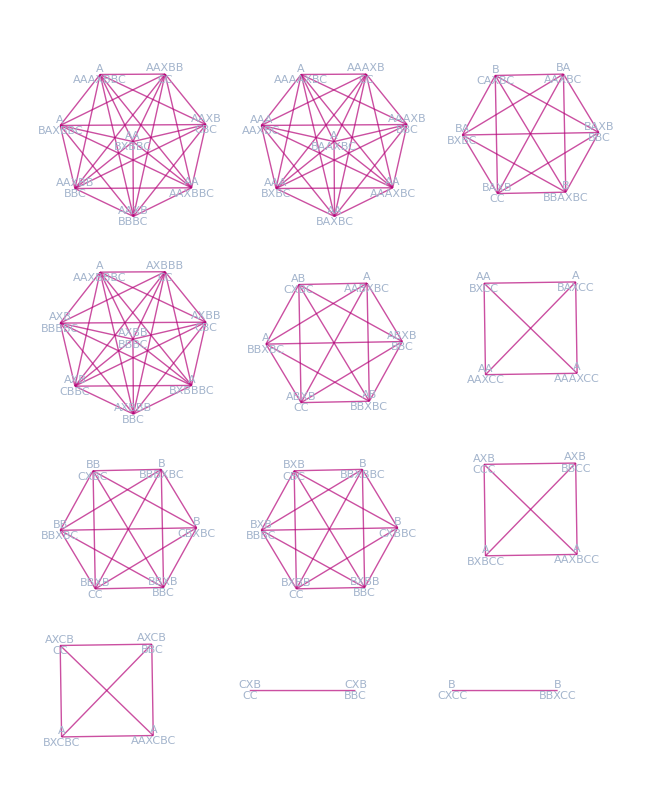

```mathematica
ResourceFunction["MultiwaySystem"][{"A"-> "B","B"-> "C","A"-> "AA","B"-> "BB"},"AXBC",3,"EventBranchialGraph"]
```

```mathematica
ResourceFunction["KnuthBendixCompletion"][{"A"-> "B","B"-> "C","C"-> "B"},"AXBC",3]
```

{AXBB→BXCB,BXCB→AXBB,AXCC→BXCB,BXCB→AXCC,BXBC→BXCB,BXCB→BXBC,BXBC→CXBB,CXBB→BXBC,BXBC→CXCC,CXCC→BXBC,BXCB→CXBB,CXBB→BXCB,BXCB→CXCC,CXCC→BXCB,CXBB→CXCC,CXCC→CXBB}

```mathematica
ResourceFunction["MultiwaySystem"][{"A"-> "B","B"-> "C","C"-> "B","AXBB"->"BXCB","BXCB"->"AXBB","AXCC"->"BXCB","BXCB"->"AXCC","BXBC"->"BXCB","BXCB"->"BXBC","BXBC"->"CXBB","CXBB"->"BXBC","BXBC"->"CXCC","CXCC"->"BXBC","BXCB"->"CXBB","CXBB"->"BXCB","BXCB"->"CXCC","CXCC"->"BXCB","CXBB"->"CXCC","CXCC"->"CXBB"},"AXBC",6,"CausalGraphInstances",MaxItems-> 5]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ResourceFunction["MultiwaySystem"][{"A"-> "B","B"-> "C","C"-> "B","C"-> "A","B"-> "A"},"StateEvolutionFunction"]
```

{}

```mathematica
ResourceFunction["CanonicalKnuthBendixCompletion"][{"A"-> "B","B"-> "C","C"-> "B","C"-> "A"}]
```

{A→B,B→A}

#### After discussion with Jonathan, what I need to do now are:

Demonstrate subsystem measurement and think about subsystem causal invariance

Look at Bell measurement in QuantumToMultiwaySystem and think about how to translate it to string

Subsystem measurement

```mathematica
ResourceFunction["MultiwaySystem"][{"A"-> "B","B"-> "A","B"-> "C","AC"-> "AB","AC"-> "AB","BC"-> "AB","BC"-> "BA", "AB"-> "BA","BA"-> "AB","CC"-> "CB","CC"-> "CA"},"AXBC",4,"EvolutionGraph"]
```

-Graphics-

```mathematica
a =ResourceFunction["MultiwaySystem"][{"A"-> "B","B"-> "A","B"-> "C","AC"-> "BB","AC"-> "AA","BC"-> "AB","BC"-> "BA","CC"-> "CB","CC"-> "CA","AB"-> "BA","BA"-> "AB"},"AXBC",5][[5]]
```

{AXAA,AXAB,AXAC,AXBA,AXBB,AXBC,AXCA,AXCB,AXCC,BXAA,BXAB,BXAC,BXBA,BXBB,BXBC,BXCA,BXCB,BXCC,CXAA,CXAB,CXAC,CXBA,CXBB,CXBC,CXCA,CXCB}

```mathematica
b = ResourceFunction["MultiwaySystem"][{"A"-> "B","B"-> "A","B"-> "C","AC"-> "AB","AC"-> "BA","BC"-> "AB","BC"-> "BA","CC"-> "CB","CC"-> "CA"},"AXBC",5][[5]]
```

{AXAA,AXAB,AXAC,AXBA,AXBB,AXBC,AXCA,AXCB,AXCC,BXAA,BXAB,BXAC,BXBA,BXBB,BXBC,BXCA,BXCB,BXCC,CXAA,CXAB,CXAC,CXBA,CXBB,CXBC,CXCA,CXCB}

```mathematica
Complement[a,b]
```

{}

```mathematica
ResourceFunction["MultiwaySystem"][{"A"-> "B","B"-> "A","B"-> "C","AC"-> "AB","AC"-> "AB","BC"-> "AB","BC"-> "BA","CC"-> "CB","CC"-> "CA"},"AXBC",3,"EvolutionGraph"]
```

-Graphics-

#### Quantum teleportation in QuantumToMultiwaySystem

```mathematica
{{a,b},{c,d}}.{{e,f},{g,h}}
```

```mathematica
{{a e+b g,a f+b h},{c e+d g,c f+d h}}
Transpose[{{a,b,c,d}}]
```

{{a e+b g,a f+b h},{c e+d g,c f+d h}}

{{a},{b},{c},{d}}

Initial State

```mathematica
BellState = {{1,0,0,1}};
message = {{α,β}};
KroneckerProduct[BellState,message]
```

{{α,β,0,0,0,0,α,β}}

Projection to one of Bell basis in BC

```mathematica
proj =Transpose[{{0,1,1,0}}].{{0,1,1,0}};
Bellmeas = KroneckerProduct[IdentityMatrix[2],proj]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
ResourceFunction["QuantumToMultiwaySystem"][Bellmeas, {{1,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,1,0,0,0,0,0,0}, {0,0,0,0,0,0,1,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,1}},1,"EvolutionGraphStructure","IncludeStatePathWeights"-> True, VertexLabels-> "VertexWeight" ]
```

-Graphics-

```mathematica
ResourceFunction["QuantumToMultiwaySystem"][Bellmeas, {{1,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,1,0,0,0,0,0,0}, {0,0,0,0,0,0,1,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,1}},1][[2]]
```

{{0, 0, 0, 0, 0, 0, 1, 0},{0, 0, 0, 0, 0, 1, 0, 0},{0, 0, 1, 0, 0, 0, 0, 0},{0, 1, 0, 0, 0, 0, 0, 0}}

```mathematica
Length[%]
```

14

2

```mathematica
ResourceFunction["QuantumToMultiwaySystem"][Bellmeas]
```

{{0, 1, 0, 0, 0, 0, 0, 0}→{0, 1, 0, 0, 0, 0, 0, 0},{0, 1, 0, 0, 0, 0, 0, 0}→{0, 0, 1, 0, 0, 0, 0, 0},{0, 0, 1, 0, 0, 0, 0, 0}→{0, 1, 0, 0, 0, 0, 0, 0},{0, 0, 1, 0, 0, 0, 0, 0}→{0, 0, 1, 0, 0, 0, 0, 0},{0, 0, 0, 0, 0, 1, 0, 0}→{0, 0, 0, 0, 0, 1, 0, 0},{0, 0, 0, 0, 0, 1, 0, 0}→{0, 0, 0, 0, 0, 0, 1, 0},{0, 0, 0, 0, 0, 0, 1, 0}→{0, 0, 0, 0, 0, 1, 0, 0},{0, 0, 0, 0, 0, 0, 1, 0}→{0, 0, 0, 0, 0, 0, 1, 0},{0, -1, 0, 0, 0, 0, 0, 0}→{0, -1, 0, 0, 0, 0, 0, 0},{0, -1, 0, 0, 0, 0, 0, 0}→{0, 0, -1, 0, 0, 0, 0, 0},{0, 0, -1, 0, 0, 0, 0, 0}→{0, -1, 0, 0, 0, 0, 0, 0},{0, 0, -1, 0, 0, 0, 0, 0}→{0, 0, -1, 0, 0, 0, 0, 0},{0, 0, 0, 0, 0, -1, 0, 0}→{0, 0, 0, 0, 0, -1, 0, 0},{0, 0, 0, 0, 0, -1, 0, 0}→{0, 0, 0, 0, 0, 0, -1, 0},{0, 0, 0, 0, 0, 0, -1, 0}→{0, 0, 0, 0, 0, -1, 0, 0},{0, 0, 0, 0, 0, 0, -1, 0}→{0, 0, 0, 0, 0, 0, -1, 0},{0, I, 0, 0, 0, 0, 0, 0}→{0, I, 0, 0, 0, 0, 0, 0},{0, I, 0, 0, 0, 0, 0, 0}→{0, 0, I, 0, 0, 0, 0, 0},{0, 0, I, 0, 0, 0, 0, 0}→{0, I, 0, 0, 0, 0, 0, 0},{0, 0, I, 0, 0, 0, 0, 0}→{0, 0, I, 0, 0, 0, 0, 0},{0, 0, 0, 0, 0, I, 0, 0}→{0, 0, 0, 0, 0, I, 0, 0},{0, 0, 0, 0, 0, I, 0, 0}→{0, 0, 0, 0, 0, 0, I, 0},{0, 0, 0, 0, 0, 0, I, 0}→{0, 0, 0, 0, 0, I, 0, 0},{0, 0, 0, 0, 0, 0, I, 0}→{0, 0, 0, 0, 0, 0, I, 0},{0, -I, 0, 0, 0, 0, 0, 0}→{0, -I, 0, 0, 0, 0, 0, 0},{0, -I, 0, 0, 0, 0, 0, 0}→{0, 0, -I, 0, 0, 0, 0, 0},{0, 0, -I, 0, 0, 0, 0, 0}→{0, -I, 0, 0, 0, 0, 0, 0},{0, 0, -I, 0, 0, 0, 0, 0}→{0, 0, -I, 0, 0, 0, 0, 0},{0, 0, 0, 0, 0, -I, 0, 0}→{0, 0, 0, 0, 0, -I, 0, 0},{0, 0, 0, 0, 0, -I, 0, 0}→{0, 0, 0, 0, 0, 0, -I, 0},{0, 0, 0, 0, 0, 0, -I, 0}→{0, 0, 0, 0, 0, -I, 0, 0},{0, 0, 0, 0, 0, 0, -I, 0}→{0, 0, 0, 0, 0, 0, -I, 0}}

```mathematica
ResourceFunction["MultiwaySystem"][{"A"->"B", "B"-> "A","C"-> "B","C"-> "A","AAB"-> "ABA", "AAB"-> "AAB","ABA"-> "ABA", "ABA"-> "AAB","BAB"-> "BBA","BAB"-> "BAB","BBA"-> "BAB","BBA"-> "BBA"},"ABC",5,"EvolutionGraph"]
```

-Graphics-

```mathematica
ResourceFunction["MultiwaySystem"][{"A"->"B", "B"-> "A"},{"AXBA","AXBB","AXBB"},4,"EvolutionGraph","IncludeStatePathWeights"-> True, VertexLabels-> "VertexWeight"]
```

-Graphics-

Basis ordering: 000,001, 010, 011, 100, 101, 110, 111 is equivalent to
                            AAA, AAB, ABA, AAB, ABB, BAA, BAB, BBA, BBB
 We can then just translate the matrix element of Bell measurement in computational basis to string basis.

```mathematica
ResourceFunction["MultiwaySystem"][{"A"->"B", "B"-> "A","C"-> "B","C"-> "A","C"-> "A"
},"ABC",4,"CausalGraphInstances",MaxItems-> 5]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ResourceFunction["MultiwaySystem"][{"A"-> "B","B"-> "A","AAB"-> "ABA", "AAB"-> "AAB","ABA"-> "ABA", "ABA"-> "AAB","BAB"-> "BBA","BAB"-> "BAB","BBA"-> "BAB","BBA"-> "BBA"},{"ABB","ABA"},3,"EvolutionGraph"]
```

-Graphics-

```mathematica
ResourceFunction["MultiwaySystem"][{"A"-> "B","B"-> "A","AAB"-> "ABA", "AAB"-> "AAB","ABA"-> "ABA", "ABA"-> "AAB","BAB"-> "BBA","BAB"-> "BAB","BBA"-> "BAB","BBA"-> "BBA"},{"AAB","AAA","AAA"},3]
```

{{AAB,AAA,AAA},{AAA,AAB,ABA,ABB,BAA,BAB},{AAA,AAB,ABA,ABB,BAA,BAB,BBA,BBB},{AAA,AAB,ABA,ABB,BAA,BAB,BBA,BBB}}

```mathematica
uju
```

```mathematica
ResourceFunction["MultiwaySystem"][{"A"-> "B","B"-> "A","AAB"-> "ABA", "AAB"-> "AAB","ABA"-> "ABA", "ABA"-> "AAB","BAB"-> "BBA","BAB"-> "BAB","BBA"-> "BAB","BBA"-> "BBA"},{"AAB","AAA"},1,"EvolutionBranchialGraph"]
```

-Graphics-

### Bell measurement on tripartite subsystem

```mathematica
BellBasis1 = {{1,0,0,1}};
BellBasis2 = {{1,0,0,-1}};
BellBasis3 = {{0,1,1,0}};
BellBasis4 ={{0,1,-1,0}};
(*Projecting BC to Bell basis in ABC*)
BellProj1 =KroneckerProduct[IdentityMatrix[2],Transpose[BellBasis1].BellBasis1]
BellProj2 =KroneckerProduct[IdentityMatrix[2],Transpose[BellBasis2].BellBasis2]//MatrixForm
BellProj3 =KroneckerProduct[IdentityMatrix[2],Transpose[BellBasis3].BellBasis3]//MatrixForm
BellProj4 =KroneckerProduct[IdentityMatrix[2],Transpose[BellBasis4].BellBasis4]//MatrixForm
```

{{1,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{1,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,1},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,1}}

(1 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 1)

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | -1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | -1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

Evolution to generate Bell state from 00

```mathematica
Hadamard = KroneckerProduct[{{1,1},{1,-1}},IdentityMatrix[2]];
CNOT = {{1,0,0,0},{0,1,0,0},{0,0,0,1},{0,0,1,0}};
GenBellState1 = KroneckerProduct[CNOT.Hadamard,IdentityMatrix[2]]
GenBellState1.Transpose[{{0,1,0,0,0,0,0,0}}]//MatrixForm
```

{{1,0,0,0,1,0,0,0},{0,1,0,0,0,1,0,0},{0,0,1,0,0,0,1,0},{0,0,0,1,0,0,0,1},{0,0,1,0,0,0,-1,0},{0,0,0,1,0,0,0,-1},{1,0,0,0,-1,0,0,0},{0,1,0,0,0,-1,0,0}}

(0
1
0
0
0
0
0
1)

```mathematica
ResourceFunction["QuantumToMultiwaySystem"][GenBellState1,{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0}},1,"IncludeStatePathWeights"-> True,VertexLabels-> "VertexWeight"]
```

{{{1, 0, 0, 0, 0, 0, 0, 0},{0, 1, 0, 0, 0, 0, 0, 0}},{{0, 0, 0, 0, 0, 0, 0, 1},{0, 0, 0, 0, 0, 0, 1, 0},{0, 1, 0, 0, 0, 0, 0, 0},{1, 0, 0, 0, 0, 0, 0, 0}}}

```mathematica
ResourceFunction["QuantumToMultiwaySystem"][CNOT.Hadamard]
```

{{1, 0, 0, 0}→{1, 0, 0, 0},{1, 0, 0, 0}→{0, 0, 0, 1},{0, 1, 0, 0}→{0, 1, 0, 0},{0, 1, 0, 0}→{0, 0, 1, 0},{0, 0, 1, 0}→{1, 0, 0, 0},{0, 0, 0, 1}→{0, 1, 0, 0},{0, 0, 1, 0}→{0, 0, 0, -1},{0, 0, 0, 1}→{0, 0, -1, 0},{0, 0, -1, 0}→{0, 0, 0, 1},{0, 0, 0, -1}→{0, 0, 1, 0},{-1, 0, 0, 0}→{-1, 0, 0, 0},{-1, 0, 0, 0}→{0, 0, 0, -1},{0, -1, 0, 0}→{0, -1, 0, 0},{0, -1, 0, 0}→{0, 0, -1, 0},{0, 0, -1, 0}→{-1, 0, 0, 0},{0, 0, 0, -1}→{0, -1, 0, 0},{I, 0, 0, 0}→{I, 0, 0, 0},{I, 0, 0, 0}→{0, 0, 0, I},{0, I, 0, 0}→{0, I, 0, 0},{0, I, 0, 0}→{0, 0, I, 0},{0, 0, I, 0}→{I, 0, 0, 0},{0, 0, 0, I}→{0, I, 0, 0},{0, 0, I, 0}→{0, 0, 0, -I},{0, 0, 0, I}→{0, 0, -I, 0},{0, 0, -I, 0}→{0, 0, 0, I},{0, 0, 0, -I}→{0, 0, I, 0},{-I, 0, 0, 0}→{-I, 0, 0, 0},{-I, 0, 0, 0}→{0, 0, 0, -I},{0, -I, 0, 0}→{0, -I, 0, 0},{0, -I, 0, 0}→{0, 0, -I, 0},{0, 0, -I, 0}→{-I, 0, 0, 0},{0, 0, 0, -I}→{0, -I, 0, 0}}

Corresponding rule AA→AA, AA→BB, AA→AXA, BB→BXB

```mathematica
ResourceFunction["MultiwaySystem"][{"AA"-> "AA", "AA"-> "BB", "AA"-> "AXA", "BB"-> "BXB"},{"AAA","AAB"},2,"StatesGraph","IncludeStatePathWeights"-> True,VertexLabels-> "VertexWeight"]
```

-Graphics-

```mathematica
ResourceFunction["MultiwaySystem"][{"AA"-> "AA","AA"-> "BB","C"-> "A","C"-> "B","AA"-> "AXA","BB"-> "BXB"},{"AAC"},3,"EvolutionGraph","IncludeStatePathWeights"-> True,VertexLabels-> "VertexWeight"]
```

-Graphics-

```mathematica
ResourceFunction["MultiwaySystem"][{"A"-> "BX","B"-> "XA","C"-> "A","C"-> "B"},{"ABC"},2]
```

{{ABC},{ABA,ABB,AXAC,BXBC},{ABBX,ABXA,AXAA,AXAB,AXBXC,BXBA,BXBB,BXXAC,XAXBC}}

```mathematica
completion = {"ABA"-> "AAA","AAA"-> "ABA", "ABA"-> "ABB","ABB"-> "ABA","AAB"-> "AAA","AAA"-> "AAB","AAB"-> "ABB","ABB"-> "AAB","BAB"-> "BAA","BAA"-> "BAB", "BAB"-> "BBB", "BBB"-> "BAB","BBA"->"BAA","BAA"-> "BBA", "BBA"-> "BBB", "BBB"-> "BBA" };
ResourceFunction["MultiwaySystem"][completion,{"AAA","AAB","ABA","ABB","BAA", "BAB", "BBA","BBB"},1,"StatesGraph"]
```

-Graphics-

```mathematica
ResourceFunction["MultiwaySystem"][Join[{"A"-> "B","B"-> "A","C"-> "A","C"-> "B"},completion],{"ABC"},3,"StatesGraph","IncludeStatePathWeights"-> True,VertexLabels-> "VertexWeight"]
```

-Graphics-

Bell measurement completion procedure to project BC to (AA+BB) from ABC

-Graphics-

```mathematica
ResourceFunction["MultiwaySystem"][Join[{"A"-> "B","B"-> "A","C"-> "A","C"-> "B"},completion],{"ABC"},3,"CausalInvariantQ"]
```

True

#### Bell measurement

```mathematica
BellProj1.Transpose[{{1,0,0,0,0,0,0,0}}]//MatrixForm
```

(1
0
0
1
0
0
0
0)

When we do projective measurement in computational basis, let’s say to the basis AA. What we do is we project AB↔AA, BA↔AA, BB↔AA. So, when we project to BellState1 (AA+BB) what we do is AB↔AA, AB↔BB, BA↔AA, BA↔BB

```mathematica
ResourceFunction["MultiwaySystem"][{"AA"-> "BB","AA"-> "AA","AB"-> "AA","AA"-> "AB", "AB"-> "BB","BB"-> "AB","BA"-> "AA","AA"-> "BA","BA"-> "BB","BB"-> "BA"},{"AAB","AAA"},2,"EvolutionGraph","IncludeStatePathWeights"-> True,VertexLabels-> "VertexWeight"]
```

-Graphics-

```mathematica
ResourceFunction["MultiwaySystem"][{"AA"-> "BB", "AA"-> "AXA", "BB"-> "BXB","AB"-> "AA","AA"-> "AB", "AB"-> "BB","BB"-> "AB","BA"-> "AA","AA"-> "BA","BA"-> "BB","BB"-> "BA"},{"AAA","AAB"},3,"CausalInvariantQ"]
```

True

```mathematica
ResourceFunction["MultiwaySystem"][{"AA"-> "BB"},{"AAB","AAA"},1,"EvolutionGraph","IncludeStatePathWeights"-> True,VertexLabels-> "VertexWeight"]
```

-Graphics-

```mathematica
stateslist=Flatten[ResourceFunction["MultiwaySystem"][{"AA"-> "BB", "AA"-> "AA","AA"-> "AXA", "BB"-> "BXB","AB"-> "AA","AA"-> "AB", "AB"-> "BB","BB"-> "AB","BA"-> "AA","AA"-> "BA","BA"-> "BB","BB"-> "BA"},{"AAA","AAB"},3,"AllStatesList"]]
```

{AAA,AAB,AAA,AAB,AAXA,ABA,ABB,AXAA,AXAB,BAA,BAB,BBA,BBB,AAA,AAB,AAXA,ABA,ABB,ABXA,ABXB,AXAA,AXAB,AXAXA,AXBA,AXBB,BAA,BAB,BAXA,BBA,BBB,BBXA,BBXB,BXBA,BXBB,AAA,AAB,AAXA,AAXB,ABA,ABB,ABXA,ABXB,AXAA,AXAB,AXAXA,AXBA,AXBB,AXBXB,BAA,BAB,BAXA,BAXB,BBA,BBB,BBXA,BBXB,BXAA,BXAB,BXBA,BXBB,BXBXA,BXBXB}

```mathematica
StringCases[stateslist,{__~~"XAA",__~~"XBB"}]
```

{{},{},{},{},{},{},{},{AXAA},{},{},{},{},{},{},{},{},{},{},{},{},{AXAA},{},{},{},{AXBB},{},{},{},{},{},{},{},{},{BXBB},{},{},{},{},{},{},{},{},{AXAA},{},{},{},{AXBB},{},{},{},{},{},{},{},{},{},{BXAA},{},{},{BXBB},{},{}}

```mathematica
KBrule = {"BBA"-> "AAA", "AAA"-> "BBA","BBA"-> "BBB","BBB"-> "BBA", "AAB"-> "AAA","AAA"-> "AAB", "AAB"-> "BBB","BBB"-> "AAB"}
KBrule2 = {"BA"-> "AA", "AA"-> "BA","BA"-> "BB","BB"-> "BA", "AB"-> "AA","AA"-> "AB", "AB"-> "BB","BB"-> "AB"}
ResourceFunction["MultiwaySystem"][{"AAA"-> "AAA", "AAA"-> "BBA", "AAB"-> "AAB", "AAB"-> "BBB"},{"AAA","AAB"},1,"EvolutionGraph"]
```

{BBA→AAA,AAA→BBA,BBA→BBB,BBB→BBA,AAB→AAA,AAA→AAB,AAB→BBB,BBB→AAB}

{BA→AA,AA→BA,BA→BB,BB→BA,AB→AA,AA→AB,AB→BB,BB→AB}

-Graphics-

```mathematica
ResourceFunction["MultiwaySystem"][Join[{"AAA"-> "AAA", "AAA"-> "BBA", "AAB"-> "AAB", "AAB"-> "BBB"},KBrule2],{"AAA","AAB"},2,"EvolutionGraph","IncludeStatePathWeights"-> True,VertexLabels-> "VertexWeight"]
```

-Graphics-

```mathematica
(CNOT.Hadamard).Transpose[{{0,0,0,1}}]
```

{{0},{1},{-1},{0}}

```mathematica
ResourceFunction["MultiwaySystem"][Join[{"AXA"-> "AXA", "AXA"-> "BXB","AXB"-> "AXB","AXB"-> "BXA","BXA"-> "AXA","BXA"-> "BXB", "BXB"-> "AXB", "BXB"->"BXA","AXA"-> "AXA", "BXB"-> "BXB","C"-> "A", "C"-> "B"  },KBrule2],"AXAC",2,"EvolutionGraph","IncludeStatePathWeights"-> True,VertexLabels-> "VertexWeight"]
```

-Graphics-

```mathematica
ResourceFunction["MultiwaySystem"][Join[{"AA"-> "AA", "AA"-> "BB","AB"-> "AB","AB"-> "BA","BA"-> "AA","BA"-> "BB", "BB"-> "AB", "BB"->"BA","AA"-> "AXA", "BB"-> "BXB","C"-> "A", "C"-> "B"  },KBrule2],"AAC",3][[3]]
```

{AAA,AAB,AAC,AAXA,ABA,ABB,ABC,AXAA,AXAB,AXAC,BAA,BAB,BAC,BBA,BBB,BBC,BXBC}